```mathematica
Ggauss[q_, z_, r_] = Sum[PDF[PoissonDistribution[z],k]*k/z*Sum[PDF[BinomialDistribution[k-1,q],m]*CDF[NormalDistribution[r,0.2],m/k], {m, 0, k-1}],{k,1,100}];
```

```mathematica
Cascade2single[z_, r_] = (SeriesCoefficient[Series[Ggauss[q,  z, r], {q, 0,2}],1]-1)^2 - 4*(SeriesCoefficient[Series[Ggauss[q,  z, r], {q, 0,2}],0]*SeriesCoefficient[Series[Ggauss[q, z, r], {q, 0,2}],2]);
```

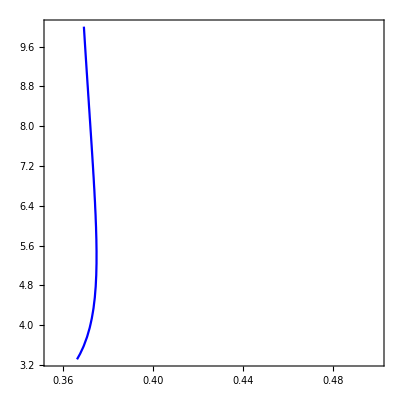

```mathematica
single = ContourPlot[(Cascade2single[z, r])==0, {r, 0.3543, 0.5}, {z,3.316,10}, ContourStyle->Directive[RGBColor[0.,0.,1.]]]
```

```mathematica
GN1gauss[q_, p_, z_, r_] = (Sum[PDF[PoissonDistribution[z],k]*k/z*Sum[PDF[BinomialDistribution[k-1,q],m]*CDF[NormalDistribution[r,0.2],m/k], {m, 0, k-1}],{k,1,100}])* (Sum[PDF[PoissonDistribution[z],k]*Sum[PDF[BinomialDistribution[k,p],w]*CDF[NormalDistribution[r,0.2],w/k], {w, 0, k}],{k,1,100}]);
```

```mathematica
CascadeNode2[z_, r_] = (SeriesCoefficient[Series[GN1gauss[q, q, z, r], {q, 0,2}],1]-1)^2 - 4*(SeriesCoefficient[Series[GN1gauss[q, q, z, r], {q, 0,2}],0]*SeriesCoefficient[Series[GN1gauss[q, q, z, r], {q, 0,2}],2]);
```

```mathematica
Cascade4[z_, r_] = SeriesCoefficient[Series[GN1gauss[q, q, z, r], {q, 0,4}],4];
```

```mathematica
deq[q_,z_, r_] = N[D[GN1gauss[q, q, z, r], {q, 1}]-1]
```

-1.+(1) 1+(2.71828^(-1. z) z (0.5 Erfc[3.53553 (-0.5+r)]-0.5 Erfc[3.53553 r])+97+1.07151×10^-156 2.71828^(-1. z) z^99 (49.5 q^98 Erfc[3.53553 (-0.99+r)]+296)) (2.71828^(-1. z) z (0.5 q Erfc[1]+1)+98+1)
 |  |  |  |

```mathematica
ddeq[q_,z_, r_] = N[D[deq[q, z, r], {q, 1}]]
```

1
 |  |  |  |

```mathematica
FindRoot[{GN1gauss[q, q, z, r] - q ==0,  deq[q, z, r] ==0, ddeq[q, z, r]==0}, {{q, 0}, {z, 1}, {r, 0.15}}]
```

{q→0.361848,z→2.47623,r→0.143785}

```mathematica
transline[z_] := N[FindRoot[{GN1gauss[q, q, z, r] == q,  deq[q, z, r] ==0}, {{q, 0}, {r, 0.2}}]][[2]]
```

```mathematica
Plot[transline[z], {z, 2.47623, 10}]
```

$Aborted

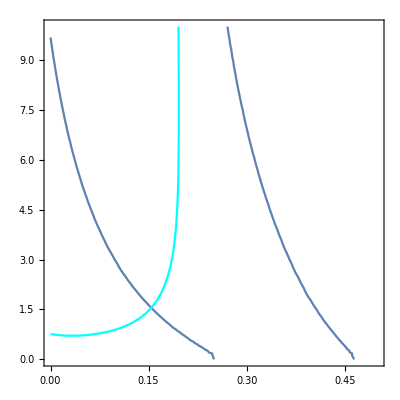

```mathematica
Show[%33, EdgeDouble]
```

```mathematica
FindRoot[{CascadeNode2[z, r]==0 ,Cascade4[z,r]==0},{{r,0.15},{z,2}}]
```

{r→0.138534,z→2.15682}

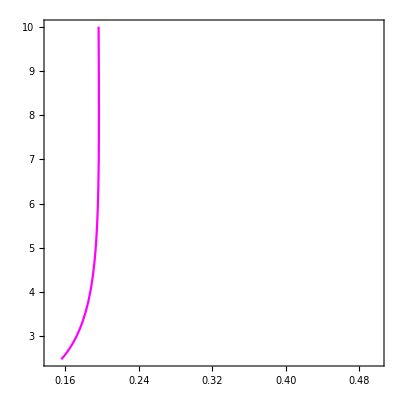

```mathematica
NodeDouble = ContourPlot[(CascadeNode2[z, r])==0 , {r, 0.143785, 0.5}, {z,2.47623,10}, ContourStyle->Directive[RGBColor[1.,0.,1.]]]
```

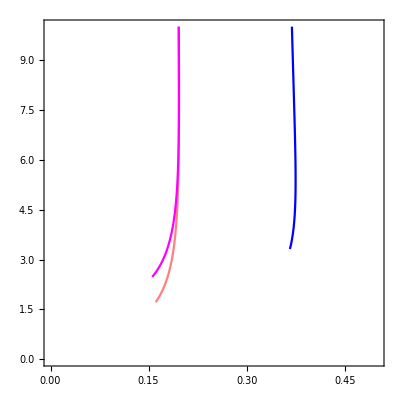

```mathematica
Show[%68, NodeDouble, single, PlotRange->{{0,0.5}, {0, 10}}]
```

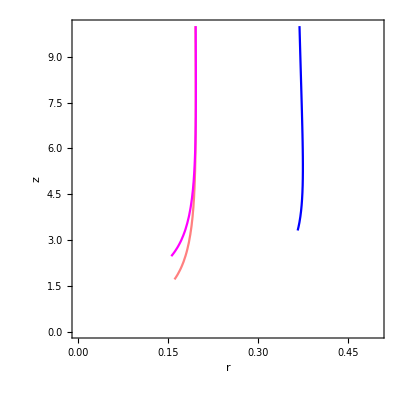

```mathematica
Show[%69,FrameLabel->{{HoldForm[z],None},{HoldForm[r],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["~/Documents/BT_MP/BT_MP/MP_doc_templates/new_figs/fullphase.eps",%70]
```

~/Documents/BT_MP/BT_MP/MP_doc_templates/new_figs/fullphase.eps

```mathematica
data=BinaryReadList["/home/user/Documents/BT_MP/BT_MP/coordination_game/simulations/hetero_node_swap_sim_2126_.dat","Real32"];
```

```mathematica
Length[data]
```

441

```mathematica
griddat = ArrayReshape[data, {21, 26}];
```

```mathematica
zcoord = Range[0., 10, 0.5];
```

```mathematica
Length[zcoord]
```

21

```mathematica
rcoord = Range[0, 0.5, 0.02];
```

```mathematica
Length[rcoord]
```

26

```mathematica
Surface= Flatten[Table[{rcoord[[j]],zcoord[[i]],griddat[[i,j]]},{j,26},{i,21}],1];
```

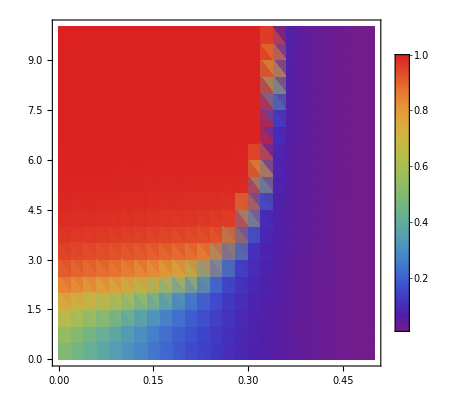

```mathematica
simulationdata = ListDensityPlot[Surface, ColorFunction->"Rainbow", PlotLegends->Automatic, ColorFunctionScaling->False]
```

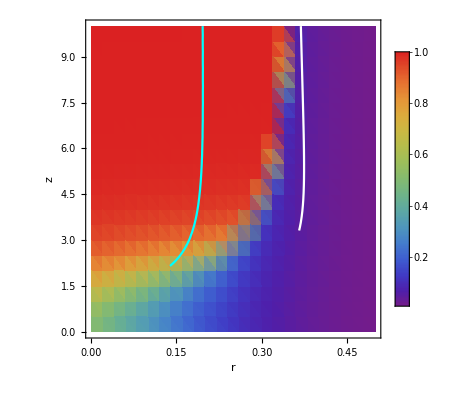

```mathematica
Finaldiagram = Show[simulationdata, single, NodeDouble , FrameLabel->{{HoldForm[z],None},{HoldForm[r],None}},LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["~/Documents/BT_MP/BT_MP/MP_doc_templates/new_figs/er_hetero_node.eps",Finaldiagram]
```

~/Documents/BT_MP/BT_MP/MP_doc_templates/new_figs/er_hetero_node.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["er_hetero_edge.eps"]]]
```